```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
If[OS=="win",
Print["Working Directory:,",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory:,",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: runNum = ",runNum={10195,10199,10207}]
(*2016:{11149,11154,11159,11162,11166,11170,11205,11208,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11331,11334,11342,11348,11351,11354,11357,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
{11149,11154,11159,11162,11166,11170,11205,11213,11214,11218,11219,11239,11243,11247,11250,11255,11263,11267,11270,11272,11276,11277,11281,11289,11292,11295,11299,11305,11325,11334,11342,11348,11351,11354,11360,11363,11366,11385,11388,11391,11395,11398,11399,11402,11405,11406,11409,11412,11416,11430,11433,11436,11439,11442,11445,11448,11453,11457,11461,11464},
2015:{10210,10219,10224,10227,10231,10239,10246,10261,10262,10264,10265,10270,10271,10273,10276,10281,10284,10286,10297,10345,10353,10357,10358,10386,10390,10391,10400,10404,10413,10415,10417,10420,10450,10451,10453,10455,10462,10463,10465,10469,10471,10472,10476,10483,10497,10541}]*)
(*Using command:$ sed'/#/d'./010195-0_UCNswitch.edm>mody.edm,*)
Print["#Runs in the list: runn = ",runn=Dimensions[runNum][[1]]];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
histbeg=100;histlast=1400;icycle=25;ChNum=4;binw=10;
histbeg2=0;
ptreal=Table[0,{k,1,runn}];
ptdat=0;
ptdat2=0;
(*6->HV, SF1->25, SF2->26,U->27,D->28,U+D->27+28,Monitor->30,TotN->32,Fill->31,RF->-1*)
```

Working Directory:,C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory:,C:\Users\tmpra\Dropbox\nEDM\rawdata

Runs in the list: runNum = {10195,10199,10207}

#Runs in the list: runn = 3

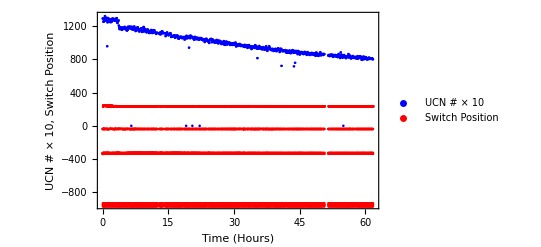

```mathematica
runnum=runNum[[3]];
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"_Meta3.edm"],metaStructure2];
dataswt=Import[StringJoin[AscDir,"\\",IntegerString[runnum,10,6],"\\",IntegerString[runnum,10,6],"-0_UCNswitch3.edm"]];
maxcy2=Dimensions[dataswt][[1]];
maxcy=data[[-1]][[2]];
ptdat2=Table[{(AbsoluteTime[dataswt[[k]][[1]]]-AbsoluteTime[dataswt[[1]][[1]]])/(3600),{dataswt[[k]][[2]],Sqrt[Abs[dataswt[[k]][[2]]]]}},{k,1,maxcy2}];
ptdat=Table[{(AbsoluteTime[data[[k]][[1]]]-AbsoluteTime[dataswt[[1]][[1]]])/(3600),{(data[[k]][[27]]+data[[k]][[28]])/10,Sqrt[data[[k]][[27]]+data[[k]][[28]]]/10}},{k,1,maxcy}];
EDAListPlot[ptdat,ptdat2,PlotLegends->{"UCN # × 10","Switch Position"},PlotStyle->{Blue,Red},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"Time (Hours)","UCN # × 10, Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]
```

```mathematica
mult=1;
j=1;i=1;ptdatcorr={};ptdat2corr={};
diffswt={};diffud={};avgswitchpos=0;
While[((i≤maxcy)&&(j≤maxcy2)),
randnum=RandomReal[];
If[(((ptdat[[i]][[1]]-ptdat2[[j]][[1]])<(100/(3600)))&&(ptdat2[[j]][[2]][[1]]≥0)&&(Abs[ptdat[[i]][[2]][[1]]-ptdat[[i-1]][[2]][[1]]]≤50)),
ptdatcorr=AppendTo[ptdatcorr,{ptdat[[i]][[1]],{N[ptdat[[i]][[2]][[1]]-(randnum*100)],ptdat[[i]][[2]][[2]]}}];
ptdat2corr=AppendTo[ptdat2corr,{ptdat2[[i]][[1]]*5,{ptdat2[[i]][[2]][[1]]-(randnum*100)+50,ptdat2[[i]][[2]][[2]]}}];
];
If[((ptdat[[i]][[1]]-ptdat2[[j]][[1]])≥(100/(3600))),
j++;,
If[((ptdat[[i]][[1]]-ptdat2[[j]][[1]])≤-(100/(3600))),
i++;,
i++;j++;
];
];
];
If[Dimensions[ptdatcorr][[1]]==Dimensions[ptdat2corr][[1]],
Print["Sorting Matches, Dimensions[ptdatcorr][[1]] = ",Dimensions[ptdatcorr][[1]]," == Dimensions[ptdat2corr][[1]] = ",Dimensions[ptdat2corr][[1]]]
,
Print["!!!!Sorting does NOT Matches, Dimensions[ptdatcorr][[1]] = ",Dimensions[ptdatcorr][[1]]," == Dimensions[ptdat2corr][[1]] = ",Dimensions[ptdat2corr][[1]]]
];
Print["Average position of filling switch: avgswitchpos = ",avgswitchpos=(-Mean[ptdat2corr[[100;;,2]][[;;,1]]]-20)];
Print["Size of sorted sets: newmaxcy = ",newmaxcy=Dimensions[ptdatcorr][[1]]];
fitucnnum=Interpolation[ptdatcorr[[100;;,2]][[;;,1]],InterpolationOrder->2];
For[i=1,i≤newmaxcy,i++,
randnum=RandomReal[];
diffswt=AppendTo[diffswt,{ptdatcorr[[i]][[1]],{.1*mult*N[(ptdat2corr[[i]][[2]][[1]]-avgswitchpos)],0.1*N[ptdat2corr[[i]][[2]][[2]]]}}];
diffud=AppendTo[diffud,{ptdatcorr[[i]][[1]],{-10*mult*Abs[(ptdatcorr[[i]][[2]][[1]]-(1230(Exp[-0.0075(i/10)])-50))/(1230(Exp[-0.0075(i/10)])-50)],N[10*ptdat2corr[[i]][[2]][[2]]/(1230(Exp[-0.0075(i/10)])-50)]}}];
];
ptdat3=Transpose[{diffswt[[;;,2]][[;;,1]],diffud[[;;,2]]}];
Show[{
(*Plot[fitucnnum[xx*10],{xx,1,newmaxcy/10},PlotRange->{{1,62},{-300,1500}},Frame->True,PlotRange->Full,FrameLabel->{"Time (Hours)","UCN # × 10, Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000}]*)
Plot[{1230(Exp[-0.0075t])-50,avgswitchpos},{t,0,60},PlotRange->{{1,51},{10,1500}},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{"Time (Hours)","UCN # × 10 , Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},Axes->False],
EDAListPlot[ptdatcorr,ptdat2corr,PlotLegends->{"(N_Up + N_Down) × 10","Switch Position"},PlotStyle->{Blue,Red},PlotRange->{{1,51},{10,1500}},Frame->True,FrameLabel->{"Time (Hours)","(N_Up + N_Down) × 10 , Switch Position"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
}]
```

Sorting Matches, Dimensions[ptdatcorr][[1]] = 599 == Dimensions[ptdat2corr][[1]] = 599

Average position of filling switch: avgswitchpos = 233.055

Size of sorted sets: newmaxcy = 599

-Graphics-

NonlinearModelFit::lmnl: The model -0.322049+mm Abs[x] is linear in the parameters {mm}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

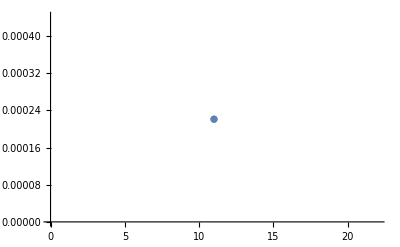

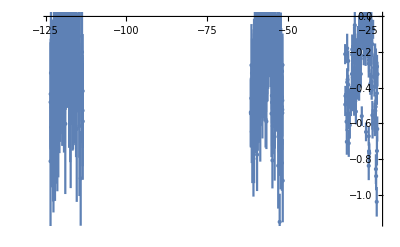

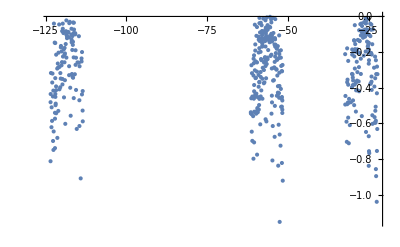

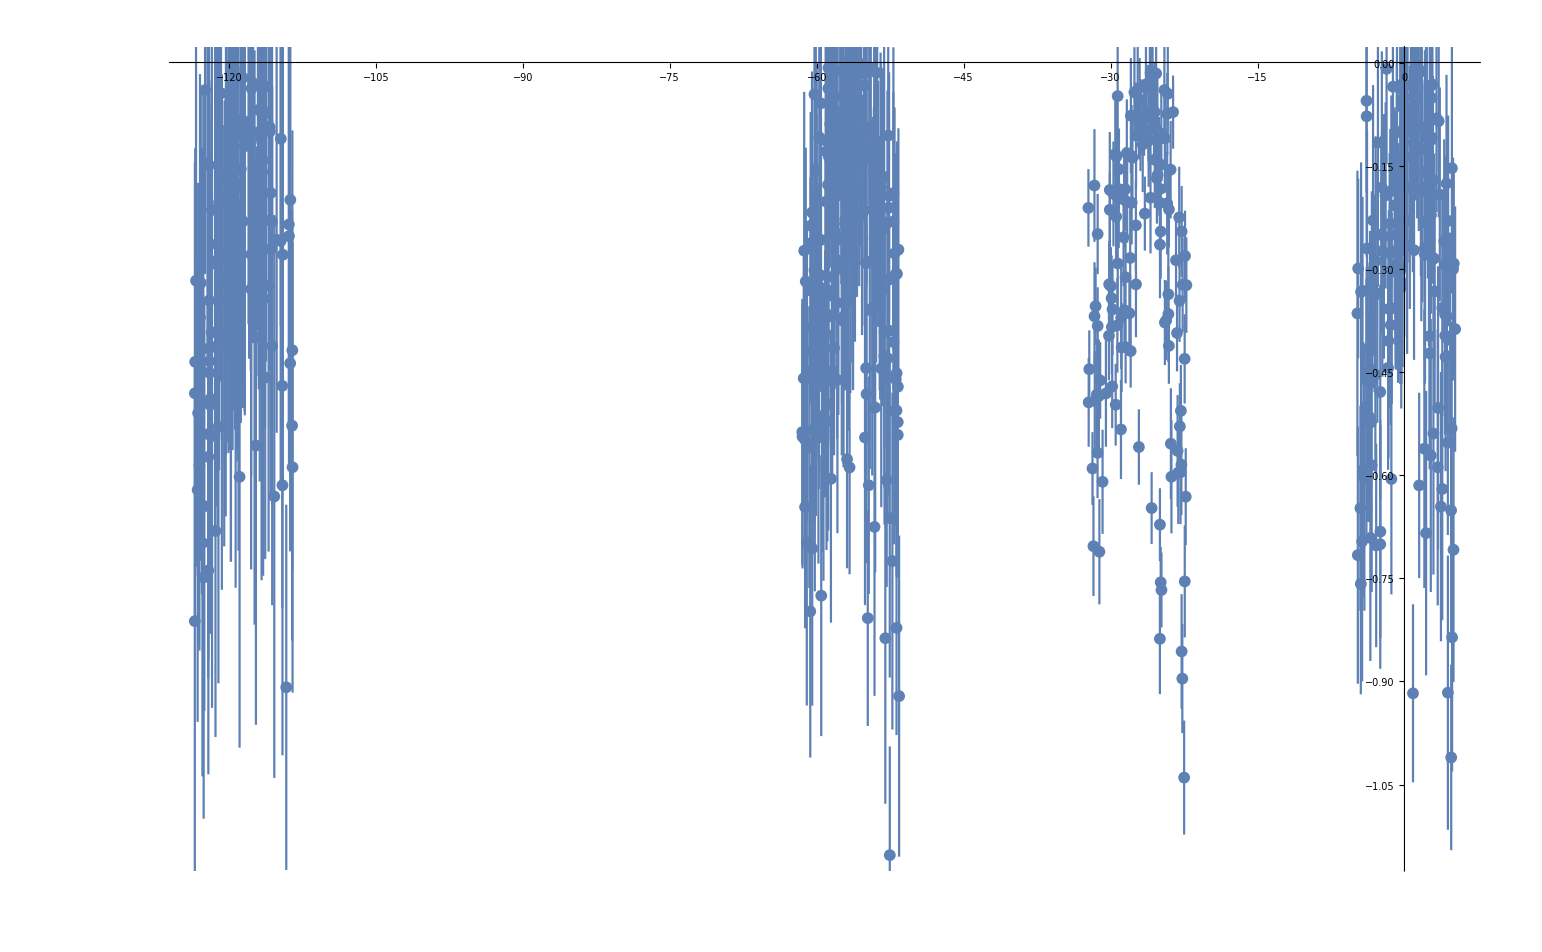

0.000221078

```mathematica
slope={};
For[k=11,k≤11,k+=.1,
plat=k;
ftdatin1=Select[ptdat3,(Abs[#[[1]]]>plat&&#[[1]]>-200)&];
ftdat1=Transpose[{ftdatin1[[;;,1]],ftdatin1[[;;,2]][[;;,1]]}];
ftdatin2=Select[ptdat3,(Abs[#[[1]]]<plat&&#[[1]]>-200)&];
ftdat2=Transpose[{ftdatin2[[;;,1]],ftdatin2[[;;,2]][[;;,1]]}];
platavg=Mean[ftdat2[[;;,2]]];
nlm=NonlinearModelFit[ftdat1,{mm Abs[x]+platavg},{{mm,-1}},x,Method->NMinimize];
slope=AppendTo[slope,{k,(mm/.nlm["BestFitParameters"])}];
];
ListPlot[slope]
EDAListPlot[ftdatin1]
ListPlot[ftdat1]
EDAListPlot[ptdat3]
Min[slope[[;;,2]]]
```

```mathematica
ptdat3[[1]]
```

{-25.8104,{-0.647887,0.0522245}}

```mathematica
sl Abs[plat]- vo
sl Abs[plat]+vo
sl Abs[plat]
```

0.0271996

-0.4022

-0.1875

| Estimate | Standard Error | t-Statistic | P-Value
mm | 0.000221078 | 0.000134184 | 1.64757 | 0.100139

0.000221078

-0.25764

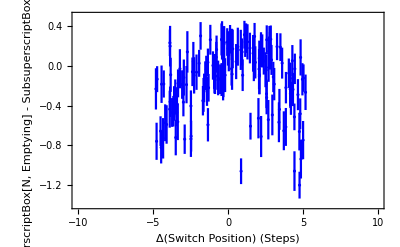

```mathematica
nlm["ParameterTable"]
plat=1.5*mult;
sl=-.125*mult;(mm/.nlm["BestFitParameters"])
vo=mult/1.25* nlm[[1]][[3]][[2]][[1]][[1]]
Show[{(*Plot[{ConditionalExpression[(Abs[xx]sl)+.21,Abs[xx]>plat],ConditionalExpression[Abs[xx]sl+ vo+.21,Abs[xx]>plat],ConditionalExpression[Abs[xx]sl- vo+.21,Abs[xx]>plat],
ConditionalExpression[sl Abs[plat]+.21,Abs[xx]<plat],ConditionalExpression[sl Abs[plat]+vo+.21,Abs[xx]<plat],ConditionalExpression[sl Abs[plat]- vo+.21,Abs[xx]<plat]},{xx,-10,10},Filling->{{2->{3}},{5->{6}}},PlotStyle->{Red,None,None,Purple,None,None},PlotRange->{mult{-10,10},mult*{-1,0.4}},Frame->True,FrameLabel->{"Δ(Switch Position) (Steps)","(N^Emptying-N_fit^Emptying)/⟨N^Emptying-N_fit^Emptying⟩ (%)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18,Black},ImageSize->{1000}],*)
EDAListPlot[Transpose[{ptdat3[[;;,1]],Transpose[{(ptdat3[[;;,2]][[;;,1]]+.21)1.5,ptdat3[[;;,2]][[;;,2]]}]}],PlotStyle->{Blue},PlotRange->{mult{-10,10},mult*{-1.4,0.5}},Frame->True,FrameLabel->{"Δ(Switch Position) (Steps)","(⟨SuperscriptBox[N, Emptying] - SubsuperscriptBox[N, fit, Emptying]⟩ - (SuperscriptBox[N, Emptying] - SubsuperscriptBox[N, fit, Emptying]))/⟨SuperscriptBox[N, Emptying] - SubsuperscriptBox[N, fit, Emptying]⟩(%)"},TicksStyle->Directive[FontSize->40],LabelStyle->{22,Black},ImageSize->{1000}]
}]
```

```mathematica
sl
```

-0.125

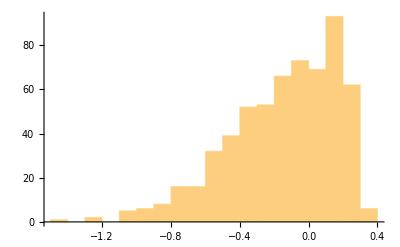

0.316179

-0.148014

```mathematica
histdat=Transpose[{ptdat3[[;;,1]],Transpose[{(ptdat3[[;;,2]][[;;,1]]+.21)1.5,ptdat3[[;;,2]][[;;,2]]}]}];
Histogram[histdat[[;;,2]][[;;,1]]]
StandardDeviation[histdat[[;;,2]][[;;,1]]]
Mean[histdat[[;;,2]][[;;,1]]]
```

## Extras

FindFit::ivar: 11.1 is not a valid variable.

FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},{1.17049,1112.3},{1.17885,1119.5},{1.18723,1099.67},{1.19567,1033.81},{1.22066,1025.74},{1.229,1084.21},{1.23738,1036.45},{1.30424,1034.68},{1.31295,1090.9},{1.32096,1031.59},{1.32929,1042.34},{1.33769,1108.3},{1.34605,1053.81},{1.35441,1071.81},{1.36277,1073.08},{1.37114,1061.46},{1.42131,1047.55},{1.4464,1088.27},{1.45475,1104.58},{1.46311,1071.88},{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},{1.63034,1020.03},{1.63868,1027.03},{1.64705,995.356},{1.65543,1023.45},{1.68048,985.857},{1.6889,996.319},{1.69721,1046.51},{1.70556,1058.95},{1.71394,1030.83},{1.72241,1073.72},{1.73065,964.026},{1.739,967.057},{1.74739,1001.38},{1.75591,1036.91},{1.76411,1059.56},{1.77247,969.933},{1.78084,1062.91},{1.78922,997.912},{1.79771,967.529},{1.80599,1043.19},{1.81431,986.906},{1.82264,1043.56},{1.85609,1044.36},{1.86443,1058.37},{1.87279,959.389},{1.88126,1031.22},{1.88954,997.076},{1.89787,978.723},{1.92299,995.94},{1.93131,959.014},{1.9397,1043.51},{1.94803,1017.61},{1.95643,1015.41},{1.96477,1045.73},{1.98986,995.64},{1.9982,1030.22},{2.00731,1023.43},{2.03165,1035.71},{2.04001,991.982},{2.06509,1012.34},{2.07345,993.858},{2.08182,1036.72},{2.09022,1000.78},{2.11526,1031.53},{2.12364,1048.56},{2.132,966.788},{2.14036,1031.46},{2.14879,976.074},{2.1571,1034.36},{2.16541,1038.49},{2.19052,994.07},{2.19891,1037.69},{2.20723,967.072},{2.23232,1000.9},{2.24069,959.331},{2.24904,978.972},{2.25746,1032.52},{2.26575,958.088},{2.27414,971.04},{2.28249,964.525},{2.29084,975.022},{2.29923,1023.},{2.30769,954.097},{2.31595,978.038},{2.32431,1015.7},{2.33277,951.566},{2.34102,944.798},{2.34935,976.917},{2.35779,940.23},{2.3661,950.442},{2.37444,1001.93},{2.3828,977.029},{2.41626,963.787},{2.42467,956.054},{2.43302,922.269},{2.44137,955.115},{2.44973,1028.4},{2.45819,1039.59},{2.4666,1039.15},{2.47483,1023.17},{2.48314,992.992},{2.49149,1004.},{2.49986,1002.44},{2.50822,1034.8},{2.51656,967.227},{2.52498,974.468},{2.53328,933.494},{2.54169,1019.23},{2.55001,987.287},{2.55837,969.506},{2.56673,926.344},{2.5751,928.858},{2.58347,969.404},{2.59182,926.89},{2.61691,996.822},{2.62527,964.298},{2.63364,962.076},{2.64199,946.136},{2.65036,939.917},{2.65875,959.098},{2.66707,961.785},{2.69223,985.998},{2.70049,1002.7},{2.70888,971.298},{2.71721,933.133},{2.7256,964.318},{2.73395,1005.51},{2.74231,992.722},{2.75067,925.32},{2.75907,912.576},{2.7674,960.957},{2.77577,978.187},{2.78417,933.759},{2.79249,933.615},{2.80084,954.897},{2.80921,962.089},{2.81754,972.697},{2.82596,997.667},{2.83429,1000.98},{2.84266,882.86},{2.85104,981.376},{2.85941,954.893},{2.86774,901.172},{2.87611,980.688},{2.88445,908.807},{2.89285,947.637},{2.90119,915.908},{2.90954,972.59},{2.9179,939.271},{2.92629,969.871},{2.93466,976.114},{2.94298,958.543},{2.95134,963.197},{2.95982,973.159},{2.96815,921.679},{2.97644,892.592},{2.9848,910.558},{2.99322,989.536},{3.0015,996.436},{3.00987,971.613},{3.01825,955.407},{3.02661,914.568},{3.03496,908.222},{3.04329,963.545},{3.05167,931.773},{3.06005,976.194},{3.0684,907.033},{3.07675,947.927},{3.10187,894.959},{3.11021,917.691},{3.11857,930.159},{3.12696,942.296},{3.13528,925.678},{3.14364,977.065},{3.15203,881.479},{3.17711,915.79},{3.20221,893.713},{3.21054,880.88},{3.2189,898.308},{3.2273,924.134},{3.23566,890.177},{3.24399,972.424},{3.25235,946.682},{3.26068,962.132},{3.26906,869.59},{3.30251,874.226},{3.31087,910.32},{3.31925,909.297},{3.32761,934.299},{3.33595,886.178},{3.34431,873.419},{3.35267,950.649},{3.36109,929.536},{3.38609,925.102},{3.39455,857.819},{3.40301,858.583},{3.41121,878.067},{3.41954,924.066},{3.42799,866.449},{3.43629,890.549},{3.46147,932.69},{3.46973,910.294},{3.4781,845.389},{3.48645,946.571},{3.49481,872.767},{3.50317,928.671},{3.51155,914.177},{3.51991,884.497},{3.5283,933.86},{3.55335,921.008},{3.56173,865.714},{3.57007,891.674},{3.57842,941.836},{3.58679,892.349},{3.59519,881.632},{3.60352,875.059},{3.62862,941.239},{3.65369,861.791},{3.66209,894.591},{3.67041,929.533},{3.67878,907.546},{3.68712,861.173},{3.71223,903.89},{3.72057,883.3},{3.72898,896.219},{3.73728,868.349},{3.74566,879.42},{3.75405,868.705},{3.76235,821.343},{3.77074,898.573},{3.77909,847.748},{3.78745,916.964},{3.79586,837.912},{3.80419,867.506},{3.81255,882.579},{3.8209,877.179},{3.8293,914.564},{3.83762,880.544},{3.86277,862.948},{3.8711,866.373},{3.87944,914.248},{3.88778,893.69},{3.91287,888.714},{3.92124,813.965},{3.92961,853.528},{3.93795,860.93},{3.94632,866.018},{3.95468,924.555},{3.96307,845.022},{3.97139,884.546},{3.97976,878.957},{3.98812,867.853},{3.99648,884.206},{4.00484,897.99},{4.01322,839.884},{4.02157,892.11},{4.02997,854.834},{4.03828,827.312},{4.04666,816.815},{4.05499,896.188},{4.0634,821.156},{4.07174,883.136},{4.0801,921.409},{4.10518,879.781},{4.11354,878.793},{4.13864,888.107},{4.14697,859.687},{4.15534,841.316},{4.16385,862.392},{4.17211,826.657},{4.18042,839.434},{4.22225,879.866},{4.23059,856.607},{4.23896,892.461},{4.24731,812.672},{4.25567,874.076},{4.26406,880.914},{4.27241,848.972},{4.28081,796.608},{4.30587,786.836},{4.31425,893.761},{4.32258,859.981},{4.33097,831.687},{4.3393,857.854},{4.34766,901.501},{4.35602,889.472},{4.36439,827.655},{4.38954,832.931},{4.41454,871.023},{4.42289,872.03},{4.43127,788.024},{4.43961,842.397},{4.448,843.749},{4.45636,786.387},{4.46471,820.561},{4.47308,838.195},{4.48154,832.96},{4.48979,815.25},{4.49819,809.216},{4.50649,854.533},{4.51489,859.878},{4.52323,795.12},{4.53164,818.26},{4.53997,801.076},{4.5483,815.284},{4.55684,826.21},{4.5651,810.845},{4.57341,820.501},{4.58178,822.672},{4.59011,808.262},{4.59851,851.355},{4.60686,795.066},{4.6152,795.528},{4.64029,783.548},{4.64866,800.77},{4.65699,800.246},{4.66549,814.009},{4.67373,819.169},{4.68209,878.417},{4.69047,795.656},{4.71558,783.806},{4.72388,778.052},{4.7323,829.413},{4.74066,816.889},{4.74897,814.695},{4.75735,795.475},{4.76571,782.459},{4.77407,872.118},{4.78246,845.961},{4.79078,805.454},{4.79919,785.43},{4.80752,761.687},{4.81587,769.821},{4.82424,832.051},{4.83262,852.244},{4.84096,790.343},{4.84935,825.386},{4.85768,785.146},{4.86609,778.244},{4.87443,749.029},{4.88276,787.436},{4.89112,798.405},{4.89956,776.982},{4.90793,777.262},{4.91621,778.232},{4.92459,820.235},{4.93296,753.05},{4.9413,786.736},{4.94965,795.726},{4.958,787.429},{4.96639,860.767},{4.97472,833.548},{4.98308,841.559},{4.99147,797.92},{4.99984,820.547},{5.00819,794.223},{5.01656,795.741},{5.04999,853.48},{5.05835,811.548},{5.06671,811.834},{5.16705,808.277},{5.17541,762.54},{5.18376,782.189},{5.19215,776.443},{5.2005,796.082},{5.22556,784.341},{5.23394,764.403},{5.24229,823.113},{5.25064,853.077},{5.25902,817.081},{5.2674,739.167},{5.27573,801.317},{5.30081,783.64},{5.3092,777.418},{5.31754,773.371},{5.3259,776.103},{5.33426,743.796},{5.34265,767.825},{5.35101,799.571},{5.35934,812.725},{5.36771,779.427},{5.37613,780.813},{5.38444,758.719},{5.3928,765.622},{5.40117,814.843},{5.40953,834.219},{5.41787,850.918},{5.42628,793.323},{5.43461,835.967},{5.44294,830.601},{5.45134,833.333},{5.45967,852.224},{5.46805,739.617},{5.47643,815.183},{5.48479,737.921},{5.49312,761.76},{5.51822,850.814},{5.52657,787.03},{5.53493,798.775},{5.54331,766.54},{5.55166,781.177},{5.56001,794.771},{5.56837,761.897},{5.57678,760.626},{5.58512,736.706},{5.59354,746.717},{5.60186,750.677},{5.61022,816.357},{5.61856,836.271},{5.62687,770.573},{5.63522,775.221},{5.64364,753.264},{5.65199,839.629},{5.66042,811.135},{5.66871,786.326},{5.67701,713.753},{5.68541,793.064},{5.71055,781.152},{5.71886,753.471},{5.72721,771.311},{5.73565,777.714},{5.74398,808.587},{5.75229,806.121},{5.79411,780.096},{5.80244,819.292},{5.81086,767.746},{5.81918,742.42},{5.82755,802.315},{5.83589,767.201},{5.84429,721.986},{5.85262,796.205},{5.86101,767.795},{5.86934,781.891},{5.87778,798.828},{5.88611,742.229},{5.89445,818.357},{5.90279,745.98},{5.91117,801.51},{5.91951,700.875},{5.92786,798.073},{5.93625,790.187},{5.94461,769.158},{5.95298,744.736},{5.96131,744.457},{5.96967,771.031},{5.97815,754.456},{5.98641,775.293},{5.99478,754.899},{6.00314,787.651},{6.01153,824.375},{6.01986,786.822},{6.0282,755.837},{6.03658,770.168},{6.04498,781.734},{6.05347,807.443},{6.06167,732.641},{6.07004,796.391},{6.07842,718.427},{6.08675,792.109},{6.09511,746.504},{6.10347,790.169},{6.11182,775.252},{6.12019,768.552},{6.12855,711.475},{6.13691,741.423},{6.14528,737.814},{6.15362,718.011},{6.16202,739.346},{6.17032,726.886},{6.17875,721.25}},a ⅇ^(-11.1 t),{{a,1200},{11.1,0.0068}},t]

ReplaceAll::reps: {FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},«20»,{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},«450»},a ⅇ^(-11.1 t),{{a,1200},{11.1,«7»}},t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a/.FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},{1.17049,1112.3},{1.17885,1119.5},{1.18723,1099.67},{1.19567,1033.81},{1.22066,1025.74},{1.229,1084.21},{1.23738,1036.45},{1.30424,1034.68},{1.31295,1090.9},{1.32096,1031.59},{1.32929,1042.34},{1.33769,1108.3},{1.34605,1053.81},{1.35441,1071.81},{1.36277,1073.08},{1.37114,1061.46},{1.42131,1047.55},{1.4464,1088.27},{1.45475,1104.58},{1.46311,1071.88},{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},{1.63034,1020.03},{1.63868,1027.03},{1.64705,995.356},{1.65543,1023.45},{1.68048,985.857},{1.6889,996.319},{1.69721,1046.51},{1.70556,1058.95},{1.71394,1030.83},{1.72241,1073.72},{1.73065,964.026},{1.739,967.057},{1.74739,1001.38},{1.75591,1036.91},{1.76411,1059.56},{1.77247,969.933},{1.78084,1062.91},{1.78922,997.912},{1.79771,967.529},{1.80599,1043.19},{1.81431,986.906},{1.82264,1043.56},{1.85609,1044.36},{1.86443,1058.37},{1.87279,959.389},{1.88126,1031.22},{1.88954,997.076},{1.89787,978.723},{1.92299,995.94},{1.93131,959.014},{1.9397,1043.51},{1.94803,1017.61},{1.95643,1015.41},{1.96477,1045.73},{1.98986,995.64},{1.9982,1030.22},{2.00731,1023.43},{2.03165,1035.71},{2.04001,991.982},{2.06509,1012.34},{2.07345,993.858},{2.08182,1036.72},{2.09022,1000.78},{2.11526,1031.53},{2.12364,1048.56},{2.132,966.788},{2.14036,1031.46},{2.14879,976.074},{2.1571,1034.36},{2.16541,1038.49},{2.19052,994.07},{2.19891,1037.69},{2.20723,967.072},{2.23232,1000.9},{2.24069,959.331},{2.24904,978.972},{2.25746,1032.52},{2.26575,958.088},{2.27414,971.04},{2.28249,964.525},{2.29084,975.022},{2.29923,1023.},{2.30769,954.097},{2.31595,978.038},{2.32431,1015.7},{2.33277,951.566},{2.34102,944.798},{2.34935,976.917},{2.35779,940.23},{2.3661,950.442},{2.37444,1001.93},{2.3828,977.029},{2.41626,963.787},{2.42467,956.054},{2.43302,922.269},{2.44137,955.115},{2.44973,1028.4},{2.45819,1039.59},{2.4666,1039.15},{2.47483,1023.17},{2.48314,992.992},{2.49149,1004.},{2.49986,1002.44},{2.50822,1034.8},{2.51656,967.227},{2.52498,974.468},{2.53328,933.494},{2.54169,1019.23},{2.55001,987.287},{2.55837,969.506},{2.56673,926.344},{2.5751,928.858},{2.58347,969.404},{2.59182,926.89},{2.61691,996.822},{2.62527,964.298},{2.63364,962.076},{2.64199,946.136},{2.65036,939.917},{2.65875,959.098},{2.66707,961.785},{2.69223,985.998},{2.70049,1002.7},{2.70888,971.298},{2.71721,933.133},{2.7256,964.318},{2.73395,1005.51},{2.74231,992.722},{2.75067,925.32},{2.75907,912.576},{2.7674,960.957},{2.77577,978.187},{2.78417,933.759},{2.79249,933.615},{2.80084,954.897},{2.80921,962.089},{2.81754,972.697},{2.82596,997.667},{2.83429,1000.98},{2.84266,882.86},{2.85104,981.376},{2.85941,954.893},{2.86774,901.172},{2.87611,980.688},{2.88445,908.807},{2.89285,947.637},{2.90119,915.908},{2.90954,972.59},{2.9179,939.271},{2.92629,969.871},{2.93466,976.114},{2.94298,958.543},{2.95134,963.197},{2.95982,973.159},{2.96815,921.679},{2.97644,892.592},{2.9848,910.558},{2.99322,989.536},{3.0015,996.436},{3.00987,971.613},{3.01825,955.407},{3.02661,914.568},{3.03496,908.222},{3.04329,963.545},{3.05167,931.773},{3.06005,976.194},{3.0684,907.033},{3.07675,947.927},{3.10187,894.959},{3.11021,917.691},{3.11857,930.159},{3.12696,942.296},{3.13528,925.678},{3.14364,977.065},{3.15203,881.479},{3.17711,915.79},{3.20221,893.713},{3.21054,880.88},{3.2189,898.308},{3.2273,924.134},{3.23566,890.177},{3.24399,972.424},{3.25235,946.682},{3.26068,962.132},{3.26906,869.59},{3.30251,874.226},{3.31087,910.32},{3.31925,909.297},{3.32761,934.299},{3.33595,886.178},{3.34431,873.419},{3.35267,950.649},{3.36109,929.536},{3.38609,925.102},{3.39455,857.819},{3.40301,858.583},{3.41121,878.067},{3.41954,924.066},{3.42799,866.449},{3.43629,890.549},{3.46147,932.69},{3.46973,910.294},{3.4781,845.389},{3.48645,946.571},{3.49481,872.767},{3.50317,928.671},{3.51155,914.177},{3.51991,884.497},{3.5283,933.86},{3.55335,921.008},{3.56173,865.714},{3.57007,891.674},{3.57842,941.836},{3.58679,892.349},{3.59519,881.632},{3.60352,875.059},{3.62862,941.239},{3.65369,861.791},{3.66209,894.591},{3.67041,929.533},{3.67878,907.546},{3.68712,861.173},{3.71223,903.89},{3.72057,883.3},{3.72898,896.219},{3.73728,868.349},{3.74566,879.42},{3.75405,868.705},{3.76235,821.343},{3.77074,898.573},{3.77909,847.748},{3.78745,916.964},{3.79586,837.912},{3.80419,867.506},{3.81255,882.579},{3.8209,877.179},{3.8293,914.564},{3.83762,880.544},{3.86277,862.948},{3.8711,866.373},{3.87944,914.248},{3.88778,893.69},{3.91287,888.714},{3.92124,813.965},{3.92961,853.528},{3.93795,860.93},{3.94632,866.018},{3.95468,924.555},{3.96307,845.022},{3.97139,884.546},{3.97976,878.957},{3.98812,867.853},{3.99648,884.206},{4.00484,897.99},{4.01322,839.884},{4.02157,892.11},{4.02997,854.834},{4.03828,827.312},{4.04666,816.815},{4.05499,896.188},{4.0634,821.156},{4.07174,883.136},{4.0801,921.409},{4.10518,879.781},{4.11354,878.793},{4.13864,888.107},{4.14697,859.687},{4.15534,841.316},{4.16385,862.392},{4.17211,826.657},{4.18042,839.434},{4.22225,879.866},{4.23059,856.607},{4.23896,892.461},{4.24731,812.672},{4.25567,874.076},{4.26406,880.914},{4.27241,848.972},{4.28081,796.608},{4.30587,786.836},{4.31425,893.761},{4.32258,859.981},{4.33097,831.687},{4.3393,857.854},{4.34766,901.501},{4.35602,889.472},{4.36439,827.655},{4.38954,832.931},{4.41454,871.023},{4.42289,872.03},{4.43127,788.024},{4.43961,842.397},{4.448,843.749},{4.45636,786.387},{4.46471,820.561},{4.47308,838.195},{4.48154,832.96},{4.48979,815.25},{4.49819,809.216},{4.50649,854.533},{4.51489,859.878},{4.52323,795.12},{4.53164,818.26},{4.53997,801.076},{4.5483,815.284},{4.55684,826.21},{4.5651,810.845},{4.57341,820.501},{4.58178,822.672},{4.59011,808.262},{4.59851,851.355},{4.60686,795.066},{4.6152,795.528},{4.64029,783.548},{4.64866,800.77},{4.65699,800.246},{4.66549,814.009},{4.67373,819.169},{4.68209,878.417},{4.69047,795.656},{4.71558,783.806},{4.72388,778.052},{4.7323,829.413},{4.74066,816.889},{4.74897,814.695},{4.75735,795.475},{4.76571,782.459},{4.77407,872.118},{4.78246,845.961},{4.79078,805.454},{4.79919,785.43},{4.80752,761.687},{4.81587,769.821},{4.82424,832.051},{4.83262,852.244},{4.84096,790.343},{4.84935,825.386},{4.85768,785.146},{4.86609,778.244},{4.87443,749.029},{4.88276,787.436},{4.89112,798.405},{4.89956,776.982},{4.90793,777.262},{4.91621,778.232},{4.92459,820.235},{4.93296,753.05},{4.9413,786.736},{4.94965,795.726},{4.958,787.429},{4.96639,860.767},{4.97472,833.548},{4.98308,841.559},{4.99147,797.92},{4.99984,820.547},{5.00819,794.223},{5.01656,795.741},{5.04999,853.48},{5.05835,811.548},{5.06671,811.834},{5.16705,808.277},{5.17541,762.54},{5.18376,782.189},{5.19215,776.443},{5.2005,796.082},{5.22556,784.341},{5.23394,764.403},{5.24229,823.113},{5.25064,853.077},{5.25902,817.081},{5.2674,739.167},{5.27573,801.317},{5.30081,783.64},{5.3092,777.418},{5.31754,773.371},{5.3259,776.103},{5.33426,743.796},{5.34265,767.825},{5.35101,799.571},{5.35934,812.725},{5.36771,779.427},{5.37613,780.813},{5.38444,758.719},{5.3928,765.622},{5.40117,814.843},{5.40953,834.219},{5.41787,850.918},{5.42628,793.323},{5.43461,835.967},{5.44294,830.601},{5.45134,833.333},{5.45967,852.224},{5.46805,739.617},{5.47643,815.183},{5.48479,737.921},{5.49312,761.76},{5.51822,850.814},{5.52657,787.03},{5.53493,798.775},{5.54331,766.54},{5.55166,781.177},{5.56001,794.771},{5.56837,761.897},{5.57678,760.626},{5.58512,736.706},{5.59354,746.717},{5.60186,750.677},{5.61022,816.357},{5.61856,836.271},{5.62687,770.573},{5.63522,775.221},{5.64364,753.264},{5.65199,839.629},{5.66042,811.135},{5.66871,786.326},{5.67701,713.753},{5.68541,793.064},{5.71055,781.152},{5.71886,753.471},{5.72721,771.311},{5.73565,777.714},{5.74398,808.587},{5.75229,806.121},{5.79411,780.096},{5.80244,819.292},{5.81086,767.746},{5.81918,742.42},{5.82755,802.315},{5.83589,767.201},{5.84429,721.986},{5.85262,796.205},{5.86101,767.795},{5.86934,781.891},{5.87778,798.828},{5.88611,742.229},{5.89445,818.357},{5.90279,745.98},{5.91117,801.51},{5.91951,700.875},{5.92786,798.073},{5.93625,790.187},{5.94461,769.158},{5.95298,744.736},{5.96131,744.457},{5.96967,771.031},{5.97815,754.456},{5.98641,775.293},{5.99478,754.899},{6.00314,787.651},{6.01153,824.375},{6.01986,786.822},{6.0282,755.837},{6.03658,770.168},{6.04498,781.734},{6.05347,807.443},{6.06167,732.641},{6.07004,796.391},{6.07842,718.427},{6.08675,792.109},{6.09511,746.504},{6.10347,790.169},{6.11182,775.252},{6.12019,768.552},{6.12855,711.475},{6.13691,741.423},{6.14528,737.814},{6.15362,718.011},{6.16202,739.346},{6.17032,726.886},{6.17875,721.25}},a ⅇ^(-11.1 t),{{a,1200},{11.1,0.0068}},t]

ReplaceAll::reps: {FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},«20»,{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},«450»},a ⅇ^(-11.1 t),{{a,1200},{11.1,«7»}},t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

b/.FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},{1.17049,1112.3},{1.17885,1119.5},{1.18723,1099.67},{1.19567,1033.81},{1.22066,1025.74},{1.229,1084.21},{1.23738,1036.45},{1.30424,1034.68},{1.31295,1090.9},{1.32096,1031.59},{1.32929,1042.34},{1.33769,1108.3},{1.34605,1053.81},{1.35441,1071.81},{1.36277,1073.08},{1.37114,1061.46},{1.42131,1047.55},{1.4464,1088.27},{1.45475,1104.58},{1.46311,1071.88},{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},{1.63034,1020.03},{1.63868,1027.03},{1.64705,995.356},{1.65543,1023.45},{1.68048,985.857},{1.6889,996.319},{1.69721,1046.51},{1.70556,1058.95},{1.71394,1030.83},{1.72241,1073.72},{1.73065,964.026},{1.739,967.057},{1.74739,1001.38},{1.75591,1036.91},{1.76411,1059.56},{1.77247,969.933},{1.78084,1062.91},{1.78922,997.912},{1.79771,967.529},{1.80599,1043.19},{1.81431,986.906},{1.82264,1043.56},{1.85609,1044.36},{1.86443,1058.37},{1.87279,959.389},{1.88126,1031.22},{1.88954,997.076},{1.89787,978.723},{1.92299,995.94},{1.93131,959.014},{1.9397,1043.51},{1.94803,1017.61},{1.95643,1015.41},{1.96477,1045.73},{1.98986,995.64},{1.9982,1030.22},{2.00731,1023.43},{2.03165,1035.71},{2.04001,991.982},{2.06509,1012.34},{2.07345,993.858},{2.08182,1036.72},{2.09022,1000.78},{2.11526,1031.53},{2.12364,1048.56},{2.132,966.788},{2.14036,1031.46},{2.14879,976.074},{2.1571,1034.36},{2.16541,1038.49},{2.19052,994.07},{2.19891,1037.69},{2.20723,967.072},{2.23232,1000.9},{2.24069,959.331},{2.24904,978.972},{2.25746,1032.52},{2.26575,958.088},{2.27414,971.04},{2.28249,964.525},{2.29084,975.022},{2.29923,1023.},{2.30769,954.097},{2.31595,978.038},{2.32431,1015.7},{2.33277,951.566},{2.34102,944.798},{2.34935,976.917},{2.35779,940.23},{2.3661,950.442},{2.37444,1001.93},{2.3828,977.029},{2.41626,963.787},{2.42467,956.054},{2.43302,922.269},{2.44137,955.115},{2.44973,1028.4},{2.45819,1039.59},{2.4666,1039.15},{2.47483,1023.17},{2.48314,992.992},{2.49149,1004.},{2.49986,1002.44},{2.50822,1034.8},{2.51656,967.227},{2.52498,974.468},{2.53328,933.494},{2.54169,1019.23},{2.55001,987.287},{2.55837,969.506},{2.56673,926.344},{2.5751,928.858},{2.58347,969.404},{2.59182,926.89},{2.61691,996.822},{2.62527,964.298},{2.63364,962.076},{2.64199,946.136},{2.65036,939.917},{2.65875,959.098},{2.66707,961.785},{2.69223,985.998},{2.70049,1002.7},{2.70888,971.298},{2.71721,933.133},{2.7256,964.318},{2.73395,1005.51},{2.74231,992.722},{2.75067,925.32},{2.75907,912.576},{2.7674,960.957},{2.77577,978.187},{2.78417,933.759},{2.79249,933.615},{2.80084,954.897},{2.80921,962.089},{2.81754,972.697},{2.82596,997.667},{2.83429,1000.98},{2.84266,882.86},{2.85104,981.376},{2.85941,954.893},{2.86774,901.172},{2.87611,980.688},{2.88445,908.807},{2.89285,947.637},{2.90119,915.908},{2.90954,972.59},{2.9179,939.271},{2.92629,969.871},{2.93466,976.114},{2.94298,958.543},{2.95134,963.197},{2.95982,973.159},{2.96815,921.679},{2.97644,892.592},{2.9848,910.558},{2.99322,989.536},{3.0015,996.436},{3.00987,971.613},{3.01825,955.407},{3.02661,914.568},{3.03496,908.222},{3.04329,963.545},{3.05167,931.773},{3.06005,976.194},{3.0684,907.033},{3.07675,947.927},{3.10187,894.959},{3.11021,917.691},{3.11857,930.159},{3.12696,942.296},{3.13528,925.678},{3.14364,977.065},{3.15203,881.479},{3.17711,915.79},{3.20221,893.713},{3.21054,880.88},{3.2189,898.308},{3.2273,924.134},{3.23566,890.177},{3.24399,972.424},{3.25235,946.682},{3.26068,962.132},{3.26906,869.59},{3.30251,874.226},{3.31087,910.32},{3.31925,909.297},{3.32761,934.299},{3.33595,886.178},{3.34431,873.419},{3.35267,950.649},{3.36109,929.536},{3.38609,925.102},{3.39455,857.819},{3.40301,858.583},{3.41121,878.067},{3.41954,924.066},{3.42799,866.449},{3.43629,890.549},{3.46147,932.69},{3.46973,910.294},{3.4781,845.389},{3.48645,946.571},{3.49481,872.767},{3.50317,928.671},{3.51155,914.177},{3.51991,884.497},{3.5283,933.86},{3.55335,921.008},{3.56173,865.714},{3.57007,891.674},{3.57842,941.836},{3.58679,892.349},{3.59519,881.632},{3.60352,875.059},{3.62862,941.239},{3.65369,861.791},{3.66209,894.591},{3.67041,929.533},{3.67878,907.546},{3.68712,861.173},{3.71223,903.89},{3.72057,883.3},{3.72898,896.219},{3.73728,868.349},{3.74566,879.42},{3.75405,868.705},{3.76235,821.343},{3.77074,898.573},{3.77909,847.748},{3.78745,916.964},{3.79586,837.912},{3.80419,867.506},{3.81255,882.579},{3.8209,877.179},{3.8293,914.564},{3.83762,880.544},{3.86277,862.948},{3.8711,866.373},{3.87944,914.248},{3.88778,893.69},{3.91287,888.714},{3.92124,813.965},{3.92961,853.528},{3.93795,860.93},{3.94632,866.018},{3.95468,924.555},{3.96307,845.022},{3.97139,884.546},{3.97976,878.957},{3.98812,867.853},{3.99648,884.206},{4.00484,897.99},{4.01322,839.884},{4.02157,892.11},{4.02997,854.834},{4.03828,827.312},{4.04666,816.815},{4.05499,896.188},{4.0634,821.156},{4.07174,883.136},{4.0801,921.409},{4.10518,879.781},{4.11354,878.793},{4.13864,888.107},{4.14697,859.687},{4.15534,841.316},{4.16385,862.392},{4.17211,826.657},{4.18042,839.434},{4.22225,879.866},{4.23059,856.607},{4.23896,892.461},{4.24731,812.672},{4.25567,874.076},{4.26406,880.914},{4.27241,848.972},{4.28081,796.608},{4.30587,786.836},{4.31425,893.761},{4.32258,859.981},{4.33097,831.687},{4.3393,857.854},{4.34766,901.501},{4.35602,889.472},{4.36439,827.655},{4.38954,832.931},{4.41454,871.023},{4.42289,872.03},{4.43127,788.024},{4.43961,842.397},{4.448,843.749},{4.45636,786.387},{4.46471,820.561},{4.47308,838.195},{4.48154,832.96},{4.48979,815.25},{4.49819,809.216},{4.50649,854.533},{4.51489,859.878},{4.52323,795.12},{4.53164,818.26},{4.53997,801.076},{4.5483,815.284},{4.55684,826.21},{4.5651,810.845},{4.57341,820.501},{4.58178,822.672},{4.59011,808.262},{4.59851,851.355},{4.60686,795.066},{4.6152,795.528},{4.64029,783.548},{4.64866,800.77},{4.65699,800.246},{4.66549,814.009},{4.67373,819.169},{4.68209,878.417},{4.69047,795.656},{4.71558,783.806},{4.72388,778.052},{4.7323,829.413},{4.74066,816.889},{4.74897,814.695},{4.75735,795.475},{4.76571,782.459},{4.77407,872.118},{4.78246,845.961},{4.79078,805.454},{4.79919,785.43},{4.80752,761.687},{4.81587,769.821},{4.82424,832.051},{4.83262,852.244},{4.84096,790.343},{4.84935,825.386},{4.85768,785.146},{4.86609,778.244},{4.87443,749.029},{4.88276,787.436},{4.89112,798.405},{4.89956,776.982},{4.90793,777.262},{4.91621,778.232},{4.92459,820.235},{4.93296,753.05},{4.9413,786.736},{4.94965,795.726},{4.958,787.429},{4.96639,860.767},{4.97472,833.548},{4.98308,841.559},{4.99147,797.92},{4.99984,820.547},{5.00819,794.223},{5.01656,795.741},{5.04999,853.48},{5.05835,811.548},{5.06671,811.834},{5.16705,808.277},{5.17541,762.54},{5.18376,782.189},{5.19215,776.443},{5.2005,796.082},{5.22556,784.341},{5.23394,764.403},{5.24229,823.113},{5.25064,853.077},{5.25902,817.081},{5.2674,739.167},{5.27573,801.317},{5.30081,783.64},{5.3092,777.418},{5.31754,773.371},{5.3259,776.103},{5.33426,743.796},{5.34265,767.825},{5.35101,799.571},{5.35934,812.725},{5.36771,779.427},{5.37613,780.813},{5.38444,758.719},{5.3928,765.622},{5.40117,814.843},{5.40953,834.219},{5.41787,850.918},{5.42628,793.323},{5.43461,835.967},{5.44294,830.601},{5.45134,833.333},{5.45967,852.224},{5.46805,739.617},{5.47643,815.183},{5.48479,737.921},{5.49312,761.76},{5.51822,850.814},{5.52657,787.03},{5.53493,798.775},{5.54331,766.54},{5.55166,781.177},{5.56001,794.771},{5.56837,761.897},{5.57678,760.626},{5.58512,736.706},{5.59354,746.717},{5.60186,750.677},{5.61022,816.357},{5.61856,836.271},{5.62687,770.573},{5.63522,775.221},{5.64364,753.264},{5.65199,839.629},{5.66042,811.135},{5.66871,786.326},{5.67701,713.753},{5.68541,793.064},{5.71055,781.152},{5.71886,753.471},{5.72721,771.311},{5.73565,777.714},{5.74398,808.587},{5.75229,806.121},{5.79411,780.096},{5.80244,819.292},{5.81086,767.746},{5.81918,742.42},{5.82755,802.315},{5.83589,767.201},{5.84429,721.986},{5.85262,796.205},{5.86101,767.795},{5.86934,781.891},{5.87778,798.828},{5.88611,742.229},{5.89445,818.357},{5.90279,745.98},{5.91117,801.51},{5.91951,700.875},{5.92786,798.073},{5.93625,790.187},{5.94461,769.158},{5.95298,744.736},{5.96131,744.457},{5.96967,771.031},{5.97815,754.456},{5.98641,775.293},{5.99478,754.899},{6.00314,787.651},{6.01153,824.375},{6.01986,786.822},{6.0282,755.837},{6.03658,770.168},{6.04498,781.734},{6.05347,807.443},{6.06167,732.641},{6.07004,796.391},{6.07842,718.427},{6.08675,792.109},{6.09511,746.504},{6.10347,790.169},{6.11182,775.252},{6.12019,768.552},{6.12855,711.475},{6.13691,741.423},{6.14528,737.814},{6.15362,718.011},{6.16202,739.346},{6.17032,726.886},{6.17875,721.25}},a ⅇ^(-11.1 t),{{a,1200},{11.1,0.0068}},t]

ReplaceAll::reps: {FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},«20»,{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},«450»},a ⅇ^(-11.1 t),{{a,1200},{11.1,«7»}},t]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

11.1/.FindFit[{{1.01999,1114.44},{1.02835,1108.67},{1.03668,1079.65},{1.04505,1131.16},{1.05346,1098.83},{1.06177,1053.74},{1.08688,1035.8},{1.09521,1108.44},{1.10357,1120.24},{1.11192,1067.56},{1.12036,1060.09},{1.12865,1032.65},{1.13704,1069.88},{1.14537,1046.62},{1.15379,1083.03},{1.16218,1105.84},{1.17049,1112.3},{1.17885,1119.5},{1.18723,1099.67},{1.19567,1033.81},{1.22066,1025.74},{1.229,1084.21},{1.23738,1036.45},{1.30424,1034.68},{1.31295,1090.9},{1.32096,1031.59},{1.32929,1042.34},{1.33769,1108.3},{1.34605,1053.81},{1.35441,1071.81},{1.36277,1073.08},{1.37114,1061.46},{1.42131,1047.55},{1.4464,1088.27},{1.45475,1104.58},{1.46311,1071.88},{1.47148,1034.27},{1.47979,1001.79},{1.48822,1083.57},{1.49657,1040.54},{1.50487,1002.1},{1.51326,1078.11},{1.54676,1103.9},{1.55511,1047.02},{1.56344,1039.12},{1.57177,1013.05},{1.58016,1048.71},{1.60524,1059.47},{1.61357,994.629},{1.62199,1040.82},{1.63034,1020.03},{1.63868,1027.03},{1.64705,995.356},{1.65543,1023.45},{1.68048,985.857},{1.6889,996.319},{1.69721,1046.51},{1.70556,1058.95},{1.71394,1030.83},{1.72241,1073.72},{1.73065,964.026},{1.739,967.057},{1.74739,1001.38},{1.75591,1036.91},{1.76411,1059.56},{1.77247,969.933},{1.78084,1062.91},{1.78922,997.912},{1.79771,967.529},{1.80599,1043.19},{1.81431,986.906},{1.82264,1043.56},{1.85609,1044.36},{1.86443,1058.37},{1.87279,959.389},{1.88126,1031.22},{1.88954,997.076},{1.89787,978.723},{1.92299,995.94},{1.93131,959.014},{1.9397,1043.51},{1.94803,1017.61},{1.95643,1015.41},{1.96477,1045.73},{1.98986,995.64},{1.9982,1030.22},{2.00731,1023.43},{2.03165,1035.71},{2.04001,991.982},{2.06509,1012.34},{2.07345,993.858},{2.08182,1036.72},{2.09022,1000.78},{2.11526,1031.53},{2.12364,1048.56},{2.132,966.788},{2.14036,1031.46},{2.14879,976.074},{2.1571,1034.36},{2.16541,1038.49},{2.19052,994.07},{2.19891,1037.69},{2.20723,967.072},{2.23232,1000.9},{2.24069,959.331},{2.24904,978.972},{2.25746,1032.52},{2.26575,958.088},{2.27414,971.04},{2.28249,964.525},{2.29084,975.022},{2.29923,1023.},{2.30769,954.097},{2.31595,978.038},{2.32431,1015.7},{2.33277,951.566},{2.34102,944.798},{2.34935,976.917},{2.35779,940.23},{2.3661,950.442},{2.37444,1001.93},{2.3828,977.029},{2.41626,963.787},{2.42467,956.054},{2.43302,922.269},{2.44137,955.115},{2.44973,1028.4},{2.45819,1039.59},{2.4666,1039.15},{2.47483,1023.17},{2.48314,992.992},{2.49149,1004.},{2.49986,1002.44},{2.50822,1034.8},{2.51656,967.227},{2.52498,974.468},{2.53328,933.494},{2.54169,1019.23},{2.55001,987.287},{2.55837,969.506},{2.56673,926.344},{2.5751,928.858},{2.58347,969.404},{2.59182,926.89},{2.61691,996.822},{2.62527,964.298},{2.63364,962.076},{2.64199,946.136},{2.65036,939.917},{2.65875,959.098},{2.66707,961.785},{2.69223,985.998},{2.70049,1002.7},{2.70888,971.298},{2.71721,933.133},{2.7256,964.318},{2.73395,1005.51},{2.74231,992.722},{2.75067,925.32},{2.75907,912.576},{2.7674,960.957},{2.77577,978.187},{2.78417,933.759},{2.79249,933.615},{2.80084,954.897},{2.80921,962.089},{2.81754,972.697},{2.82596,997.667},{2.83429,1000.98},{2.84266,882.86},{2.85104,981.376},{2.85941,954.893},{2.86774,901.172},{2.87611,980.688},{2.88445,908.807},{2.89285,947.637},{2.90119,915.908},{2.90954,972.59},{2.9179,939.271},{2.92629,969.871},{2.93466,976.114},{2.94298,958.543},{2.95134,963.197},{2.95982,973.159},{2.96815,921.679},{2.97644,892.592},{2.9848,910.558},{2.99322,989.536},{3.0015,996.436},{3.00987,971.613},{3.01825,955.407},{3.02661,914.568},{3.03496,908.222},{3.04329,963.545},{3.05167,931.773},{3.06005,976.194},{3.0684,907.033},{3.07675,947.927},{3.10187,894.959},{3.11021,917.691},{3.11857,930.159},{3.12696,942.296},{3.13528,925.678},{3.14364,977.065},{3.15203,881.479},{3.17711,915.79},{3.20221,893.713},{3.21054,880.88},{3.2189,898.308},{3.2273,924.134},{3.23566,890.177},{3.24399,972.424},{3.25235,946.682},{3.26068,962.132},{3.26906,869.59},{3.30251,874.226},{3.31087,910.32},{3.31925,909.297},{3.32761,934.299},{3.33595,886.178},{3.34431,873.419},{3.35267,950.649},{3.36109,929.536},{3.38609,925.102},{3.39455,857.819},{3.40301,858.583},{3.41121,878.067},{3.41954,924.066},{3.42799,866.449},{3.43629,890.549},{3.46147,932.69},{3.46973,910.294},{3.4781,845.389},{3.48645,946.571},{3.49481,872.767},{3.50317,928.671},{3.51155,914.177},{3.51991,884.497},{3.5283,933.86},{3.55335,921.008},{3.56173,865.714},{3.57007,891.674},{3.57842,941.836},{3.58679,892.349},{3.59519,881.632},{3.60352,875.059},{3.62862,941.239},{3.65369,861.791},{3.66209,894.591},{3.67041,929.533},{3.67878,907.546},{3.68712,861.173},{3.71223,903.89},{3.72057,883.3},{3.72898,896.219},{3.73728,868.349},{3.74566,879.42},{3.75405,868.705},{3.76235,821.343},{3.77074,898.573},{3.77909,847.748},{3.78745,916.964},{3.79586,837.912},{3.80419,867.506},{3.81255,882.579},{3.8209,877.179},{3.8293,914.564},{3.83762,880.544},{3.86277,862.948},{3.8711,866.373},{3.87944,914.248},{3.88778,893.69},{3.91287,888.714},{3.92124,813.965},{3.92961,853.528},{3.93795,860.93},{3.94632,866.018},{3.95468,924.555},{3.96307,845.022},{3.97139,884.546},{3.97976,878.957},{3.98812,867.853},{3.99648,884.206},{4.00484,897.99},{4.01322,839.884},{4.02157,892.11},{4.02997,854.834},{4.03828,827.312},{4.04666,816.815},{4.05499,896.188},{4.0634,821.156},{4.07174,883.136},{4.0801,921.409},{4.10518,879.781},{4.11354,878.793},{4.13864,888.107},{4.14697,859.687},{4.15534,841.316},{4.16385,862.392},{4.17211,826.657},{4.18042,839.434},{4.22225,879.866},{4.23059,856.607},{4.23896,892.461},{4.24731,812.672},{4.25567,874.076},{4.26406,880.914},{4.27241,848.972},{4.28081,796.608},{4.30587,786.836},{4.31425,893.761},{4.32258,859.981},{4.33097,831.687},{4.3393,857.854},{4.34766,901.501},{4.35602,889.472},{4.36439,827.655},{4.38954,832.931},{4.41454,871.023},{4.42289,872.03},{4.43127,788.024},{4.43961,842.397},{4.448,843.749},{4.45636,786.387},{4.46471,820.561},{4.47308,838.195},{4.48154,832.96},{4.48979,815.25},{4.49819,809.216},{4.50649,854.533},{4.51489,859.878},{4.52323,795.12},{4.53164,818.26},{4.53997,801.076},{4.5483,815.284},{4.55684,826.21},{4.5651,810.845},{4.57341,820.501},{4.58178,822.672},{4.59011,808.262},{4.59851,851.355},{4.60686,795.066},{4.6152,795.528},{4.64029,783.548},{4.64866,800.77},{4.65699,800.246},{4.66549,814.009},{4.67373,819.169},{4.68209,878.417},{4.69047,795.656},{4.71558,783.806},{4.72388,778.052},{4.7323,829.413},{4.74066,816.889},{4.74897,814.695},{4.75735,795.475},{4.76571,782.459},{4.77407,872.118},{4.78246,845.961},{4.79078,805.454},{4.79919,785.43},{4.80752,761.687},{4.81587,769.821},{4.82424,832.051},{4.83262,852.244},{4.84096,790.343},{4.84935,825.386},{4.85768,785.146},{4.86609,778.244},{4.87443,749.029},{4.88276,787.436},{4.89112,798.405},{4.89956,776.982},{4.90793,777.262},{4.91621,778.232},{4.92459,820.235},{4.93296,753.05},{4.9413,786.736},{4.94965,795.726},{4.958,787.429},{4.96639,860.767},{4.97472,833.548},{4.98308,841.559},{4.99147,797.92},{4.99984,820.547},{5.00819,794.223},{5.01656,795.741},{5.04999,853.48},{5.05835,811.548},{5.06671,811.834},{5.16705,808.277},{5.17541,762.54},{5.18376,782.189},{5.19215,776.443},{5.2005,796.082},{5.22556,784.341},{5.23394,764.403},{5.24229,823.113},{5.25064,853.077},{5.25902,817.081},{5.2674,739.167},{5.27573,801.317},{5.30081,783.64},{5.3092,777.418},{5.31754,773.371},{5.3259,776.103},{5.33426,743.796},{5.34265,767.825},{5.35101,799.571},{5.35934,812.725},{5.36771,779.427},{5.37613,780.813},{5.38444,758.719},{5.3928,765.622},{5.40117,814.843},{5.40953,834.219},{5.41787,850.918},{5.42628,793.323},{5.43461,835.967},{5.44294,830.601},{5.45134,833.333},{5.45967,852.224},{5.46805,739.617},{5.47643,815.183},{5.48479,737.921},{5.49312,761.76},{5.51822,850.814},{5.52657,787.03},{5.53493,798.775},{5.54331,766.54},{5.55166,781.177},{5.56001,794.771},{5.56837,761.897},{5.57678,760.626},{5.58512,736.706},{5.59354,746.717},{5.60186,750.677},{5.61022,816.357},{5.61856,836.271},{5.62687,770.573},{5.63522,775.221},{5.64364,753.264},{5.65199,839.629},{5.66042,811.135},{5.66871,786.326},{5.67701,713.753},{5.68541,793.064},{5.71055,781.152},{5.71886,753.471},{5.72721,771.311},{5.73565,777.714},{5.74398,808.587},{5.75229,806.121},{5.79411,780.096},{5.80244,819.292},{5.81086,767.746},{5.81918,742.42},{5.82755,802.315},{5.83589,767.201},{5.84429,721.986},{5.85262,796.205},{5.86101,767.795},{5.86934,781.891},{5.87778,798.828},{5.88611,742.229},{5.89445,818.357},{5.90279,745.98},{5.91117,801.51},{5.91951,700.875},{5.92786,798.073},{5.93625,790.187},{5.94461,769.158},{5.95298,744.736},{5.96131,744.457},{5.96967,771.031},{5.97815,754.456},{5.98641,775.293},{5.99478,754.899},{6.00314,787.651},{6.01153,824.375},{6.01986,786.822},{6.0282,755.837},{6.03658,770.168},{6.04498,781.734},{6.05347,807.443},{6.06167,732.641},{6.07004,796.391},{6.07842,718.427},{6.08675,792.109},{6.09511,746.504},{6.10347,790.169},{6.11182,775.252},{6.12019,768.552},{6.12855,711.475},{6.13691,741.423},{6.14528,737.814},{6.15362,718.011},{6.16202,739.346},{6.17032,726.886},{6.17875,721.25}},a ⅇ^(-11.1 t),{{a,1200},{11.1,0.0068}},t]

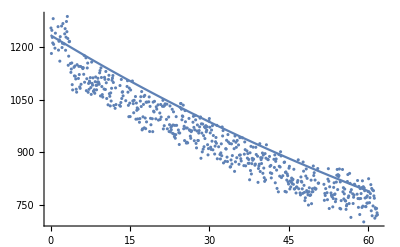

```mathematica
fitucnnum=FindFit[Transpose[{ptdatcorr[[100;;,1]]/10,ptdatcorr[[100;;,2]][[;;,1]]}],a(Exp[-k t]),{{a,1200},{k,0.0068}},t]
a/.fitucnnum
b/.fitucnnum
k/.fitucnnum
Show[{
ListPlot[Transpose[{ptdatcorr[[;;,1]],ptdatcorr[[;;,2]][[;;,1]]}]],
Plot[1230(Exp[-0.0075t])+5,{t,0,60}]
}]
```

## Test-Play

```mathematica
L=18;R=5.6;t=18(2 Pi/360);
L t < R
(4NIntegrate[Sqrt[R^2-x^2],{x,L t/2,R}]-R^2Pi)/(R^2Pi)
```

False

-0.614391

```mathematica
R^2Pi
```

98.5203